# DBSCAN

## Theme

```mathematica
fontLabels=Directive[FontFamily->"Libertinus Serif",FontSize->22];
fontTicks=Directive[FontFamily->"Libertinus Serif",FontSize->18];

(* https://mathematica.stackexchange.com/questions/54545/is-it-possible-to-define-a-new-plottheme *)
Begin["System`PlotThemeDump`"];
Themes`ThemeRules;(*preload Theme system*)

resolvePlotTheme["myThemeBasic",def:_String]:=Themes`SetWeight[
Join[
{ImageSize->Large},
{LabelStyle->fontLabels},
{TicksStyle->fontTicks},
{FrameTicksStyle->fontTicks},
(* 102 is the default grey level of Mathematica *)
{AxesStyle->Directive[AbsoluteThickness[0.3],GrayLevel[102/255]]}
]
,$ComponentWeight];
resolvePlotTheme["myTheme",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Directive[PointSize[0.013],Thick]}
]
,$ComponentWeight];
resolvePlotTheme["myThemeBW",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myTheme",def],
{PlotStyle->Thread@Directive[{GrayLevel[0.2],GrayLevel[0.8]},Thick,{Automatic,Dashed}]}
]
,$ComponentWeight];
(* Do not adjust point sizes for region plots *)
resolvePlotTheme["myTheme",def:"RegionPlot"]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Automatic}
]
,$ComponentWeight];

End[];

it[var_]:=Style[var,FontSlant->Italic]
bf[var_]:=Style[var,FontWeight->Bold]
bi[var_]:=bf[it[var]]
```

## Data

```mathematica
data={
{1,1},{0,0},{0,2},{0,2/3},{0,4/3},
{2,1},
{4,0},{4,2},{3,1},{3.5,0.5},{4,2.8}
};
```

```mathematica
padding=1.9;
plotRange={MinMax[data[[;;,1]]]+{-padding,padding},MinMax[data[[;;,2]]]+{-padding,padding}};
createClusterPlot[ϵ_,nMin_]:=ListPlot[
FindClusters[data,Method->{"DBSCAN","NeighborhoodRadius"->ϵ,"NeighborsNumber"->nMin}],
PlotTheme->"myTheme",
PlotRange->plotRange,
AspectRatio->Automatic,
AxesLabel->{it["x"],it["y"]},
Epilog->{
Opacity[0],
EdgeForm[Thick],
Table[Disk[p,ϵ],{p,data}]
}
]
```

```mathematica
Manipulate[
createClusterPlot[ϵ,4]
,{ϵ,0.1,3}]
```

## Example

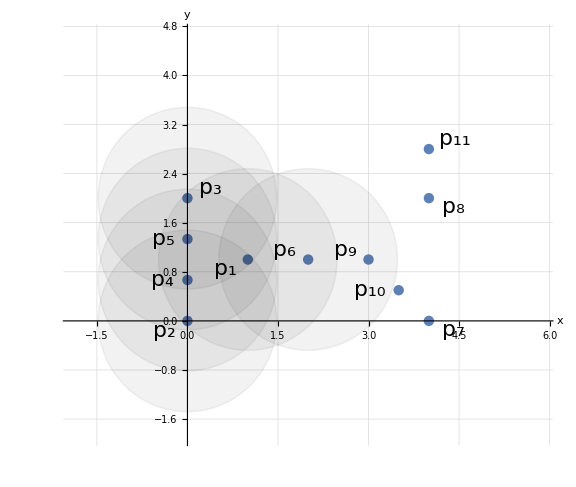

```mathematica
plotExample=Show[
ListPlot[MapThread[(Callout[#1,Subscript[bi["p"],#2]]&),{data,Range[Length[data]]}],
PlotRange->{MinMax[data[[;;,1]]]+{-padding,padding},MinMax[data[[;;,2]]]+{-padding,padding}},
AspectRatio->Automatic,
GridLines->Automatic,
PlotTheme->"myTheme",
AxesLabel->{it["x"],it["y"]}
],
Graphics[{
Opacity[0.05],
EdgeForm[Thickness[0.002]],
Table[Disk[p,1.48],{p,data[[1;;6,;;]]}]
}]
]
```

```mathematica
vertexStyle[expr_,pos_]:=Module[{},
If[expr=="",
Return[{}]
];

{Text[
Framed[expr,
Background->GrayLevel[0.9],
RoundingRadius->50,
FrameMargins->{{10,10},{12,6}},
FrameStyle->Thickness[0.01]
],pos]}
]
labels=(Subscript[bi["p"],#]&)/@Range[Length[data]];

createTreePlot[edges_]:=Module[{t,fEdges},
t=0;
fEdges={{""->labels[[edges[[1,1]]]],Row[{it["t"]," = "<>ToString[t]}]}};
Do[
t++;
AppendTo[fEdges,{labels[[e[[1]]]]->labels[[e[[2]]]],Row[{it["t"]," = "<>ToString[t]}]}];
,{e,edges}];

TreePlot[fEdges,Top,"",
VertexLabeling->True,
DirectedEdges->True,
VertexRenderingFunction->(vertexStyle[#2,#1]&),
PlotStyle->Directive[FontFamily->"Libertinus Serif",FontSize->22],
PlotRangePadding->None,
ImageSize->Automatic
]
]
```

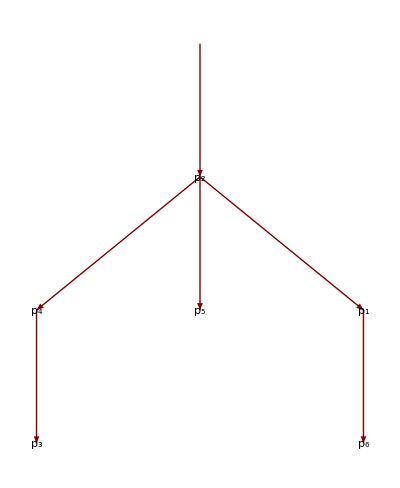

```mathematica
plotTree=createTreePlot[{2->4,2->5,2->1,4->3,1->6}]
```

## Part 1: Remaining Algorithm

From the point p_9 we reach 4 other points. However, each of these neighbours has not enough points in its own neighbourhood so that the tree does not grow further.

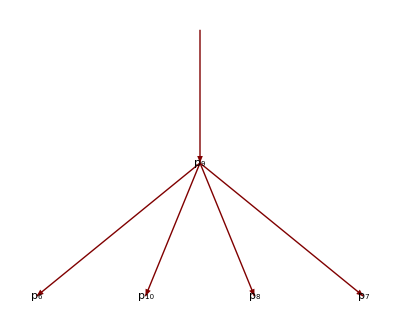

```mathematica
createTreePlot[{9->6,9->10,9->8,9->7}]
```

So, we have C_2={p_9,p_6,p_10,p_8,p_7} and the point p_11 is a noise point.

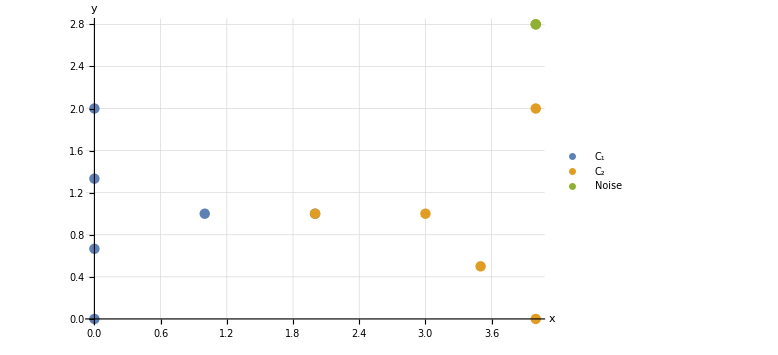

```mathematica
ListPlot[{
data[[{2,4,5,1,3,6}]],
data[[{9,6,10,8,7}]],
data[[{11}]]
},
PlotLegends->PointLegend[97,{"C_1","C_2","Noise"},LegendMarkerSize->15],
PlotTheme->"myTheme",
GridLines->Automatic,
AxesLabel->{it["x"],it["y"]}
]
```

## Part 2: Ambiguity

The point p_6 may be added to the first or the second cluster depending on the ordering of the seed points. This is possible for every border point. In the end, we may get different results when applying the DBSCAN algorithm multiple times.

## Part 3: New Parameters

With the new parameters, we get four clusters and two noise points. It is to note that both parameters have a high influence on the clustering result.

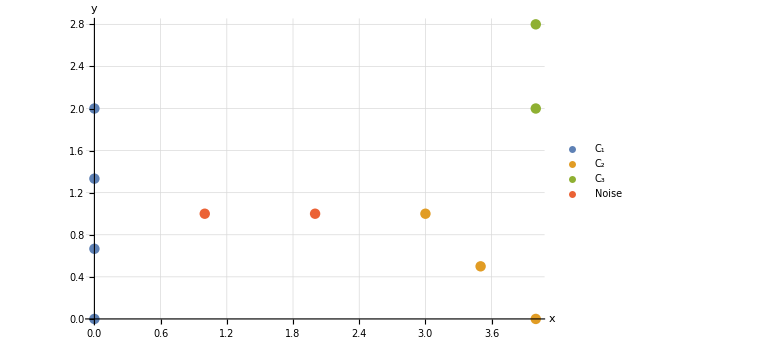

```mathematica
ListPlot[{
data[[{2,4,5,3}]],
data[[{9,10,7}]],
data[[{8,11}]],
data[[{1,6}]]
},
PlotLegends->PointLegend[97,{"C_1","C_2","C_3","Noise"},LegendMarkerSize->15],
PlotTheme->"myTheme",
GridLines->Automatic,
AxesLabel->{it["x"],it["y"]}
]
```

## Part 4: Comparison

Both algorithms are non-deterministic. However, the results differ probably more with k-means due to the random initialization of the first cluster centroids. In DBSCAN, only the border points may vary.

k-means is centroid- and DBSCAN density-based. Also, k-means minimizes the variance criterion.

Only one iteration is required for DBSCAN (then all points must have a label or are considered noise) whereas k-means requires usually multiple iterations.

Only DBSCAN can detect noise points. If k-means should be applied on a noisy dataset, the fuzzy version may be appropriate (cf. future exercise).

## Part 5: Smiley Face dataset

k-means fails on this dataset since it does not have the usual blob-like structure. What is more, a centroid does not make much sense for this kind of cluster (especially the outer ring).